```mathematica
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{200,1,80,0.3,30000,1000}];
Subscript[R, lqr]=DiagonalMatrix[{0.25,100}];
Subscript[L, 0]=0.15;Subscript[Q, 0]=90;
Get["VMCsolution.m",Path->NotebookDirectory[]]
(*====================系统参数配置====================*)
(*重力加速度*)
g=9.81;
(*连杆长度*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.270;Subscript[L, 3]=0.270;Subscript[L, 4]=0.150;Subscript[L, 5]=0.150;
(*五连杆的质量分布参数*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.135660;Subscript[l, 3]=0.135150;Subscript[l, 4]=0.064820;
Subscript[J, 1]=0.003993;Subscript[J, 2]=0.064379;Subscript[J, 3]=0.060525;Subscript[J, 4]=0.003993;
Subscript[m, 1]=0.211*2;Subscript[m, 2]=0.390*2;Subscript[m, 3]=0.204*2;Subscript[m, 4]=0.211*2;
(*机体的质量分布参数*)
Subscript[L, b]=0.01;(*机体质心相对于关节电机轴平面的高度*)
Subscript[J, b]=0.2997272;(*机体的转动惯量*)
Subscript[m, b]=8.548;(*机体的质量*)
(*驱动轮电机的质量分布参数*)
Subscript[J, wm]=0.000813;
Subscript[m, wm]=0.10*2;(*壳0.1 电机0.38*)
(*驱动轮的质量分布参数*)
Subscript[J, w]=0.004301;(*轮子的转动惯量*)
Subscript[m, w]=0.63*2;(*驱动轮的质量 0.35*)
Subscript[R, w]=0.06;(*轮的半径*)
(*====================求解等效腿的质量分布====================*)
{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4]}=VMCInverseSolution[Subscript[L, 0],Subscript[Q, 0],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]}][[3]];
(*得各质心矢量*)
Subscript[r, 1]={Subscript[l, 1] Cos[Subscript[q, 1]],Subscript[l, 1] Sin[Subscript[q, 1]]};
Subscript[r, 2]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[l, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[l, 2] Sin[Subscript[q, 2]]};
Subscript[r, 3]={Subscript[L, 4] Cos[Subscript[q, 4]]+Subscript[l, 3] Cos[Subscript[q, 3]]+Subscript[L, 5],Subscript[L, 4] Sin[Subscript[q, 4]]+Subscript[l, 3] Sin[Subscript[q, 3]]};
Subscript[r, 4]={Subscript[l, 4] Cos[Subscript[q, 4]]+Subscript[L, 5],Subscript[l, 4] Sin[Subscript[q, 4]]};
Subscript[r, w]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[L, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[L, 2] Sin[Subscript[q, 2]]};
Subscript[m, l]=Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]+Subscript[m, 4]+Subscript[m, wm];
M=Subscript[m, l]+Subscript[m, w]+Subscript[m, b];
Subscript[r, com]=Collect[Expand[Subscript[m, 1] Subscript[r, 1]+Subscript[m, 2] Subscript[r, 2]+Subscript[m, 3] Subscript[r, 3]+Subscript[m, 4] Subscript[r, 4]+Subscript[m, wm] Subscript[r, w]],{Cos[Subscript[q, 1]],Sin[Subscript[q, 1]],Cos[Subscript[q, 2]],Sin[Subscript[q, 2]],Cos[Subscript[q, 3]],Sin[Subscript[q, 3]],Cos[Subscript[q, 4]],Sin[Subscript[q, 4]]}]/Subscript[m, l];
(*求解转动惯量*)
Subscript[d, c1]=Norm[Subscript[r, 1]-Subscript[r, com]];Subscript[J, c1]=Subscript[J, 1]+Subscript[m, 1] Subscript[d, c1]^2;
Subscript[d, c2]=Norm[Subscript[r, 2]-Subscript[r, com]];Subscript[J, c2]=Subscript[J, 2]+Subscript[m, 2] Subscript[d, c2]^2;
Subscript[d, c3]=Norm[Subscript[r, 3]-Subscript[r, com]];Subscript[J, c3]=Subscript[J, 3]+Subscript[m, 3] Subscript[d, c3]^2;
Subscript[d, c4]=Norm[Subscript[r, 4]-Subscript[r, com]];Subscript[J, c4]=Subscript[J, 4]+Subscript[m, 4] Subscript[d, c4]^2;
Subscript[d, cwm]=Norm[Subscript[r, w]-Subscript[r, com]];Subscript[J, cwm]=Subscript[J, wm]+Subscript[m, wm] Subscript[d, cwm]^2;
Subscript[J, com]=Subscript[J, c1]+Subscript[J, c2]+Subscript[J, c3]+Subscript[J, c4]+Subscript[J, cwm];
(*====================腿部模型参数传递====================*)
Subscript[J, l]=Subscript[J, com];
Subscript[L, l]=Subscript[L, 0]-Norm[Subscript[r, com]-{Subscript[L, 5]/2,0}];(*腿的质心的高度*)
(*====================导入模型====================*)
θ=(Subscript[Q, 0]-90)/180*Pi;
Subscript[A, op] = Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op] = Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[C, op] = DiagonalMatrix[{1,1,1,1,1,1}];
Subscript[D, op] = ConstantArray[0,{6,2}];
(*====================LQR控制====================*)
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr]
```

{{10.3231,12.4845,47.4892,7.05029,320.63,57.1039},{-1.31666,-1.76065,-12.1285,-1.65716,7.01747,2.03044}}

```mathematica
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{1,1200,50,1,12000,1}];
Subscript[R, lqr]=DiagonalMatrix[{2,10}];
(*====================系统参数配置====================*)
(*重力加速度*)
g=9.81;
(*连杆长度*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.270;Subscript[L, 3]=0.270;Subscript[L, 4]=0.150;Subscript[L, 5]=0.150;
(*五连杆的质量分布参数*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.135660;Subscript[l, 3]=0.135150;Subscript[l, 4]=0.064820;
Subscript[J, 1]=0.003993;Subscript[J, 2]=0.064379;Subscript[J, 3]=0.060525;Subscript[J, 4]=0.003993;
Subscript[m, 1]=0.211*2;Subscript[m, 2]=0.390*2;Subscript[m, 3]=0.204*2;Subscript[m, 4]=0.211*2;
(*机体的质量分布参数*)
Subscript[L, b]=0.01;(*机体质心相对于关节电机轴平面的高度*)
Subscript[J, b]=0.2997272;(*机体的转动惯量*)
Subscript[m, b]=8.548;(*机体的质量*)
(*驱动轮电机的质量分布参数*)
Subscript[J, wm]=0.000813;
Subscript[m, wm]=0.10*2;(*壳0.1 电机0.38*)
(*驱动轮的质量分布参数*)
Subscript[J, w]=0.004301;(*轮子的转动惯量*)
Subscript[m, w]=0.63*2;(*驱动轮的质量 0.35*)
Subscript[R, w]=0.06;(*轮的半径*)
(*限位*)
upLimit=-23.41;(*上限位*)
downLimit=67.89;(*下限位*)
(*电机半径--画图*)
Subscript[R, jm]=0.045;(*GO8010*)
Subscript[R, wm]=0.0675;(*MF9025*)
(*Save[NotebookDirectory[]<>"\\VMCsolution.m",VMCForwardSolution,VMCInverseSolution];*)
Get["VMCsolution.m",Path->NotebookDirectory[]]
SystemCalcu[L0_,Q0_]:=(
Module[{},
Subscript[L, 0]=L0;
{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4]}=VMCInverseSolution[L0,Q0,{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]}][[3]];
(*====================求解等效腿的质量分布====================*)
(*得各质心矢量*)
Subscript[r, 1]={Subscript[l, 1] Cos[Subscript[q, 1]],Subscript[l, 1] Sin[Subscript[q, 1]]};
Subscript[r, 2]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[l, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[l, 2] Sin[Subscript[q, 2]]};
Subscript[r, 3]={Subscript[L, 4] Cos[Subscript[q, 4]]+Subscript[l, 3] Cos[Subscript[q, 3]]+Subscript[L, 5],Subscript[L, 4] Sin[Subscript[q, 4]]+Subscript[l, 3] Sin[Subscript[q, 3]]};
Subscript[r, 4]={Subscript[l, 4] Cos[Subscript[q, 4]]+Subscript[L, 5],Subscript[l, 4] Sin[Subscript[q, 4]]};
Subscript[r, w]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[L, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[L, 2] Sin[Subscript[q, 2]]};
Subscript[m, l]=Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]+Subscript[m, 4]+Subscript[m, wm];
M=Subscript[m, l]+Subscript[m, w]+Subscript[m, b];
Subscript[r, com]=Collect[Expand[Subscript[m, 1] Subscript[r, 1]+Subscript[m, 2] Subscript[r, 2]+Subscript[m, 3] Subscript[r, 3]+Subscript[m, 4] Subscript[r, 4]+Subscript[m, wm] Subscript[r, w]],{Cos[Subscript[q, 1]],Sin[Subscript[q, 1]],Cos[Subscript[q, 2]],Sin[Subscript[q, 2]],Cos[Subscript[q, 3]],Sin[Subscript[q, 3]],Cos[Subscript[q, 4]],Sin[Subscript[q, 4]]}]/Subscript[m, l];
(*求解转动惯量*)
Subscript[d, c1]=Norm[Subscript[r, 1]-Subscript[r, com]];Subscript[J, c1]=Subscript[J, 1]+Subscript[m, 1] Subscript[d, c1]^2;
Subscript[d, c2]=Norm[Subscript[r, 2]-Subscript[r, com]];Subscript[J, c2]=Subscript[J, 2]+Subscript[m, 2] Subscript[d, c2]^2;
Subscript[d, c3]=Norm[Subscript[r, 3]-Subscript[r, com]];Subscript[J, c3]=Subscript[J, 3]+Subscript[m, 3] Subscript[d, c3]^2;
Subscript[d, c4]=Norm[Subscript[r, 4]-Subscript[r, com]];Subscript[J, c4]=Subscript[J, 4]+Subscript[m, 4] Subscript[d, c4]^2;
Subscript[d, cwm]=Norm[Subscript[r, w]-Subscript[r, com]];Subscript[J, cwm]=Subscript[J, wm]+Subscript[m, wm] Subscript[d, cwm]^2;
Subscript[J, com]=Subscript[J, c1]+Subscript[J, c2]+Subscript[J, c3]+Subscript[J, c4]+Subscript[J, cwm];
(*====================腿部模型参数传递====================*)
Subscript[J, l]=Subscript[J, com];
Subscript[L, l]=Subscript[L, 0]-Norm[Subscript[r, com]-{Subscript[L, 5]/2,0}];(*腿的质心的高度*)
(*====================导入模型====================*)
θ=(Q0-90)/180*Pi;
Subscript[A, op] = Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op] = Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[C, op] = DiagonalMatrix[{1,1,1,1,1,1}];
Subscript[D, op] = ConstantArray[0,{6,2}];
(*====================LQR控制====================*)
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr];
Return[Subscript[K, lqr]];
];
);
Manipulate[SystemCalcu[L0,Q0],{{L0,0.2},0.1,0.4},{{Q0,90},180,0}](*显示具体数值*)
```

{7.68012-1.69684 x-43.5662 x^2+60.9093 x^3,16.6469-10.8331 x-65.3342 x^2+99.5026 x^3,34.3366+210.496 x-865.873 x^2+917.825 x^3,7.23228+7.25271 x-34.6399 x^2+34.5094 x^3,36.9872+98.2124 x-20.8582 x^2-124.761 x^3,5.55616+45.199 x-46.6075 x^2+0.556525 x^3,-0.607925-0.846185 x-0.984613 x^2+2.89844 x^3,-1.50394-0.423433 x-6.27517 x^2+10.0366 x^3,-6.2951-44.5144 x+57.9034 x^2-34.2354 x^3,-1.42809+0.334929 x-13.2375 x^2+12.7807 x^3,6.72881-7.2875 x-15.4735 x^2+28.3466 x^3,2.56242-5.24235 x+3.84217 x^2+0.0953686 x^3}

{{7.68012,-1.69684,-43.5662,60.9093},{16.6469,-10.8331,-65.3342,99.5026},{34.3366,210.496,-865.873,917.825},{7.23228,7.25271,-34.6399,34.5094},{36.9872,98.2124,-20.8582,-124.761},{5.55616,45.199,-46.6075,0.556525},{-0.607925,-0.846185,-0.984613,2.89844},{-1.50394,-0.423433,-6.27517,10.0366},{-6.2951,-44.5144,57.9034,-34.2354},{-1.42809,0.334929,-13.2375,12.7807},{6.72881,-7.2875,-15.4735,28.3466},{2.56242,-5.24235,3.84217,0.0953686}}

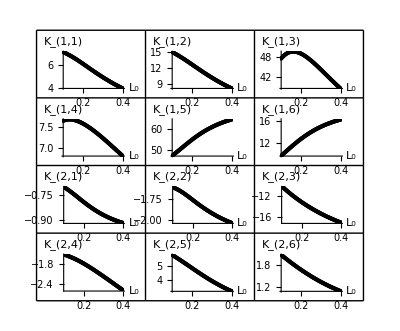

```mathematica
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{100,200,500,10,5000,300}];
Subscript[R, lqr]=DiagonalMatrix[{1,100}];
Get["VMCsolution.m",Path->NotebookDirectory[]]
(*=============================================系统参数配置=============================================*)
(*重力加速度*)
g=9.81;
(*连杆长度*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.270;Subscript[L, 3]=0.270;Subscript[L, 4]=0.150;Subscript[L, 5]=0.150;
(*五连杆的质量分布参数*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.135660;Subscript[l, 3]=0.135150;Subscript[l, 4]=0.064820;
Subscript[J, 1]=0.003993;Subscript[J, 2]=0.064379;Subscript[J, 3]=0.060525;Subscript[J, 4]=0.003993;
Subscript[m, 1]=0.211*2;Subscript[m, 2]=0.390*2;Subscript[m, 3]=0.204*2;Subscript[m, 4]=0.211*2;
(*机体的质量分布参数*)
Subscript[L, b]=0.01;(*机体质心相对于关节电机轴平面的高度*)
Subscript[J, b]=0.2997272;(*机体的转动惯量*)
Subscript[m, b]=8.548;(*机体的质量*)
(*驱动轮电机的质量分布参数*)
Subscript[J, wm]=0.000813;
Subscript[m, wm]=0.10*2;(*壳0.1 电机0.38*)
(*驱动轮的质量分布参数*)
Subscript[J, w]=0.004301;(*轮子的转动惯量*)
Subscript[m, w]=0.63*2;(*驱动轮的质量 0.35*)
Subscript[R, w]=0.06;(*轮的半径*)
(*=============================================开始循环迭代============================================*)
sampleNum=101;(*循环次数*)
paramNum=12;(*变量个数*)
Kt=Array[0,{sampleNum}];
Lt=Array[0,{sampleNum}];
Do[
(*输入量控制*)
Subscript[L, 0]=0.10+0.3*(cnt)/sampleNum;
Subscript[Q, 0]=90;
(*=========================================求解等效腿的质量分布====================================*)
{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4]}=VMCInverseSolution[Subscript[L, 0],Subscript[Q, 0],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]}][[3]];
(*得各质心矢量*)
Subscript[r, 1]={Subscript[l, 1] Cos[Subscript[q, 1]],Subscript[l, 1] Sin[Subscript[q, 1]]};
Subscript[r, 2]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[l, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[l, 2] Sin[Subscript[q, 2]]};
Subscript[r, 3]={Subscript[L, 4] Cos[Subscript[q, 4]]+Subscript[l, 3] Cos[Subscript[q, 3]]+Subscript[L, 5],Subscript[L, 4] Sin[Subscript[q, 4]]+Subscript[l, 3] Sin[Subscript[q, 3]]};
Subscript[r, 4]={Subscript[l, 4] Cos[Subscript[q, 4]]+Subscript[L, 5],Subscript[l, 4] Sin[Subscript[q, 4]]};
Subscript[r, w]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[L, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[L, 2] Sin[Subscript[q, 2]]};
Subscript[m, l]=Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]+Subscript[m, 4]+Subscript[m, wm];
M=Subscript[m, l]+Subscript[m, w]+Subscript[m, b];
Subscript[r, com]=Collect[Expand[Subscript[m, 1] Subscript[r, 1]+Subscript[m, 2] Subscript[r, 2]+Subscript[m, 3] Subscript[r, 3]+Subscript[m, 4] Subscript[r, 4]+Subscript[m, wm] Subscript[r, w]],{Cos[Subscript[q, 1]],Sin[Subscript[q, 1]],Cos[Subscript[q, 2]],Sin[Subscript[q, 2]],Cos[Subscript[q, 3]],Sin[Subscript[q, 3]],Cos[Subscript[q, 4]],Sin[Subscript[q, 4]]}]/Subscript[m, l];
(*求解转动惯量*)
Subscript[d, c1]=Norm[Subscript[r, 1]-Subscript[r, com]];Subscript[J, c1]=Subscript[J, 1]+Subscript[m, 1] Subscript[d, c1]^2;
Subscript[d, c2]=Norm[Subscript[r, 2]-Subscript[r, com]];Subscript[J, c2]=Subscript[J, 2]+Subscript[m, 2] Subscript[d, c2]^2;
Subscript[d, c3]=Norm[Subscript[r, 3]-Subscript[r, com]];Subscript[J, c3]=Subscript[J, 3]+Subscript[m, 3] Subscript[d, c3]^2;
Subscript[d, c4]=Norm[Subscript[r, 4]-Subscript[r, com]];Subscript[J, c4]=Subscript[J, 4]+Subscript[m, 4] Subscript[d, c4]^2;
Subscript[d, cwm]=Norm[Subscript[r, w]-Subscript[r, com]];Subscript[J, cwm]=Subscript[J, wm]+Subscript[m, wm] Subscript[d, cwm]^2;
Subscript[J, com]=Subscript[J, c1]+Subscript[J, c2]+Subscript[J, c3]+Subscript[J, c4]+Subscript[J, cwm];
(*============================================腿部模型参数传递====================================*)
Subscript[J, l]=Subscript[J, com];
Subscript[L, l]=Subscript[L, 0]-Norm[Subscript[r, com]-{Subscript[L, 5]/2,0}];(*腿的质心的高度*)
(*============================================导入模型============================================*)
θ=(Subscript[Q, 0]-90)/180*Pi;
α=0;
Subscript[A, op] = Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op] = Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[C, op] = DiagonalMatrix[{1,1,1,1,1,1}];
Subscript[D, op] = ConstantArray[0,{6,2}];
(*============================================LQR控制============================================*)
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr];
(*============================================数据记录===========================================*)
Kt[[cnt]] = Subscript[K, lqr];
Lt[[cnt]] = Subscript[L, 0];
,{cnt,sampleNum}];
(*============================================多项式拟合============================================*)
(*提取同一参数在不同条件下的值*)
kArray=Array[0,{paramNum}];Do[Do[kArray[[(i-1)*6+j]]=Kt[[All,i,j]],{j,6}],{i,2}];	
(*将条件值与参数值配对*)
Kxy=Array[0,{paramNum,sampleNum}];
Do[Do[Kxy[[i,j]]={Lt[[j]],kArray[[i,j]]},{j,sampleNum}],{i,paramNum}];	
(*分别对各个参数进行多项式拟合*)
Kpoly = Array[0, {paramNum}];
Do[Kpoly[[i]]= Fit[Kxy[[i]],{1,x,x^2,x^3},x],{i,paramNum}];
Kpoly
(*将多项式系数整合成一个矩阵*)
kPolyMatrix = Array[0,{12}];
Do[kPolyMatrix[[i]]=CoefficientList[Kpoly[[i]],x],{i,paramNum}];
(*多项式拟合曲线*)
KT = Array[0, {paramNum}];
Do[KT[[plotcnt]] = Plot[Kpoly[[plotcnt]], {x, Lt[[1]], Lt[[sampleNum]]}, Epilog->Point[Kxy[[plotcnt]]],Axes->{True,True}, AxesLabel->{"L_0", Subscript[K, 1,plotcnt]}],{plotcnt, 1, 6}];
Do[KT[[plotcnt]] = Plot[Kpoly[[plotcnt]], {x, Lt[[1]], Lt[[sampleNum]]}, Epilog->Point[Kxy[[plotcnt]]],Axes->{True,True}, AxesLabel->{"L_0", Subscript[K, 2,plotcnt-6]}],{plotcnt, 7, 12}];
KL0Graph = GraphicsGrid[{{KT [[1]],KT [[2]],KT [[3]]},{KT [[4]],KT [[5]],KT [[6]]},
	{KT [[7]],KT [[8]],KT [[9]]},{KT [[10]],KT [[11]],KT [[12]]}}, Frame->All,ImageSize->Full];
(*============================================数据输出===========================================*)
Print[kPolyMatrix];(*拟合多项式升幂排列*)
Show[KL0Graph](*多项式拟合曲线图*)
```

```mathematica
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{100,200,500,10,5000,300}];
Subscript[R, lqr]=DiagonalMatrix[{1,100}];
Get["VMCsolution.m",Path->NotebookDirectory[]]
(*=============================================系统参数配置=============================================*)
(*重力加速度*)
g=9.81;
(*连杆长度*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.270;Subscript[L, 3]=0.270;Subscript[L, 4]=0.150;Subscript[L, 5]=0.150;
(*五连杆的质量分布参数*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.135660;Subscript[l, 3]=0.135150;Subscript[l, 4]=0.064820;
Subscript[J, 1]=0.003993;Subscript[J, 2]=0.064379;Subscript[J, 3]=0.060525;Subscript[J, 4]=0.003993;
Subscript[m, 1]=0.211*2;Subscript[m, 2]=0.390*2;Subscript[m, 3]=0.204*2;Subscript[m, 4]=0.211*2;
(*机体的质量分布参数*)
Subscript[L, b]=0.01;(*机体质心相对于关节电机轴平面的高度*)
Subscript[J, b]=0.2997272;(*机体的转动惯量*)
Subscript[m, b]=8.548;(*机体的质量*)
(*驱动轮电机的质量分布参数*)
Subscript[J, wm]=0.000813;
Subscript[m, wm]=0.10*2;(*壳0.1 电机0.38*)
(*驱动轮的质量分布参数*)
Subscript[J, w]=0.004301;(*轮子的转动惯量*)
Subscript[m, w]=0.63*2;(*驱动轮的质量 0.35*)
Subscript[R, w]=0.06;(*轮的半径*)
(*=============================================开始循环迭代============================================*)
sampleNum=51;(*循环次数*)
paramNum=12;(*变量个数*)
Kt=Array[0,{sampleNum,sampleNum}];
Xt=Array[0,{sampleNum,sampleNum}];
Do[
Do[
(*输入量控制*)
Subscript[L, 0]=0.10+0.2*(cnt1)/sampleNum;
Subscript[Q, 0]=40+100*(cnt2)/sampleNum;
(*=========================================求解等效腿的质量分布====================================*)
{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4]}=VMCInverseSolution[Subscript[L, 0],Subscript[Q, 0],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]}][[3]];
(*得各质心矢量*)
Subscript[r, 1]={Subscript[l, 1] Cos[Subscript[q, 1]],Subscript[l, 1] Sin[Subscript[q, 1]]};
Subscript[r, 2]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[l, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[l, 2] Sin[Subscript[q, 2]]};
Subscript[r, 3]={Subscript[L, 4] Cos[Subscript[q, 4]]+Subscript[l, 3] Cos[Subscript[q, 3]]+Subscript[L, 5],Subscript[L, 4] Sin[Subscript[q, 4]]+Subscript[l, 3] Sin[Subscript[q, 3]]};
Subscript[r, 4]={Subscript[l, 4] Cos[Subscript[q, 4]]+Subscript[L, 5],Subscript[l, 4] Sin[Subscript[q, 4]]};
Subscript[r, w]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[L, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[L, 2] Sin[Subscript[q, 2]]};
Subscript[m, l]=Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]+Subscript[m, 4]+Subscript[m, wm];
M=Subscript[m, l]+Subscript[m, w]+Subscript[m, b];
Subscript[r, com]=Collect[Expand[Subscript[m, 1] Subscript[r, 1]+Subscript[m, 2] Subscript[r, 2]+Subscript[m, 3] Subscript[r, 3]+Subscript[m, 4] Subscript[r, 4]+Subscript[m, wm] Subscript[r, w]],{Cos[Subscript[q, 1]],Sin[Subscript[q, 1]],Cos[Subscript[q, 2]],Sin[Subscript[q, 2]],Cos[Subscript[q, 3]],Sin[Subscript[q, 3]],Cos[Subscript[q, 4]],Sin[Subscript[q, 4]]}]/Subscript[m, l];
(*求解转动惯量*)
Subscript[d, c1]=Norm[Subscript[r, 1]-Subscript[r, com]];Subscript[J, c1]=Subscript[J, 1]+Subscript[m, 1] Subscript[d, c1]^2;
Subscript[d, c2]=Norm[Subscript[r, 2]-Subscript[r, com]];Subscript[J, c2]=Subscript[J, 2]+Subscript[m, 2] Subscript[d, c2]^2;
Subscript[d, c3]=Norm[Subscript[r, 3]-Subscript[r, com]];Subscript[J, c3]=Subscript[J, 3]+Subscript[m, 3] Subscript[d, c3]^2;
Subscript[d, c4]=Norm[Subscript[r, 4]-Subscript[r, com]];Subscript[J, c4]=Subscript[J, 4]+Subscript[m, 4] Subscript[d, c4]^2;
Subscript[d, cwm]=Norm[Subscript[r, w]-Subscript[r, com]];Subscript[J, cwm]=Subscript[J, wm]+Subscript[m, wm] Subscript[d, cwm]^2;
Subscript[J, com]=Subscript[J, c1]+Subscript[J, c2]+Subscript[J, c3]+Subscript[J, c4]+Subscript[J, cwm];
(*============================================腿部模型参数传递====================================*)
Subscript[J, l]=Subscript[J, com];
Subscript[L, l]=Subscript[L, 0]-Norm[Subscript[r, com]-{Subscript[L, 5]/2,0}];(*腿的质心的高度*)
(*============================================导入模型============================================*)
θ=(Subscript[Q, 0]-90)/180*Pi;
Subscript[A, op] = Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op] = Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[C, op] = DiagonalMatrix[{1,1,1,1,1,1}];
Subscript[D, op] = ConstantArray[0,{6,2}];
(*============================================LQR控制============================================*)
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr];
(*============================================数据记录===========================================*)
Kt[[cnt1,cnt2]] = Subscript[K, lqr];
Xt[[cnt1,cnt2]]={Subscript[L, 0],Subscript[Q, 0]};
,{cnt1,sampleNum}];
,{cnt2,sampleNum}];
(*============================================多项式拟合============================================*)
(*提取同一参数在不同条件下的值*)
kArray=Array[0,{paramNum}];Do[Do[kArray[[(i-1)*6+j]]=Kt[[All,All,i,j]],{j,6}],{i,2}];
(*将条件值与参数值配对*)
Kxy=Array[0,{paramNum,sampleNum*sampleNum}];
Do[Do[Do[Kxy[[i,(j-1)*sampleNum+k]]={Xt[[j,k,1]],Xt[[j,k,2]],kArray[[i,j,k]]},{k,sampleNum}],{j,sampleNum}],{i,paramNum}];
(*分别对各个参数进行多项式拟合*)
Kpoly = Array[0, {paramNum}];
Do[Kpoly[[i]]= Fit[Kxy[[i]],{1,x,x^2,x^3,y,y^2,y^3,x*y,x^2*y,x*y^2},{x,y}],{i,paramNum}];
(*将多项式系数整合成一个矩阵*)
kPolyMatrix = Array[0,{12}];
Do[kPolyMatrix[[i]]=CoefficientList[Kpoly[[i]],{x,y}],{i,paramNum}];
(*多项式拟合曲线*)
KT = Array[0, {paramNum}];
KTT=Array[0,{paramNum}];
Do[KT[[plotcnt]] = Plot3D[Kpoly[[plotcnt]], {x, Xt[[1,1,1]], Xt[[sampleNum,sampleNum,1]]},{y, Xt[[1,1,2]], Xt[[sampleNum,sampleNum,2]]},Axes->{True,True,True}, AxesLabel->{"L_0", "Q_0",Subscript[K, 1,plotcnt]}];
KTT[[plotcnt]]=ListPlot3D[Kxy[[plotcnt]]],{plotcnt, 1, 6}];
Do[KT[[plotcnt]] = Plot3D[Kpoly[[plotcnt]],{x, Xt[[1,1,1]], Xt[[sampleNum,sampleNum,1]]},{y, Xt[[1,1,2]], Xt[[sampleNum,sampleNum,2]]}, Axes->{True,True,True}, AxesLabel->{"L_0", "Q_0",Subscript[K, 2,plotcnt-6]}];
KTT[[plotcnt]]=ListPlot3D[Kxy[[plotcnt]]],{plotcnt, 7, 12}];
KL0Graph = GraphicsGrid[{{KT[[1]],KT[[2]],KT[[3]]},{KT[[4]],KT[[5]],KT[[6]]},
	{KT[[7]],KT[[8]],KT[[9]]},{KT[[10]],KT[[11]],KT[[12]]}}, Frame->All,ImageSize->Full];
KLTGraph = GraphicsGrid[{{KT[[1]],KTT[[1]]},{KT[[2]],KTT[[2]]},{KT[[3]],KTT[[3]]},{KT[[4]],KTT[[4]]},{KT[[5]],KTT[[5]]},{KT[[6]],KTT[[6]]},{KT[[7]],KTT[[7]]},{KT[[8]],KTT[[8]]},{KT[[9]],KTT[[9]]},{KT[[10]],KTT[[10]]},{KT[[11]],KTT[[11]]},{KT[[12]],KTT[[12]]}}, Frame->All,ImageSize->Full];
(*============================================数据输出===========================================*)
Print[kPolyMatrix];(*拟合多项式升幂排列*)
Show[KL0Graph]
Show[KLTGraph]
(*多项式拟合曲线图*)
```

{{{3.77231,0.10665,-0.000734326,1.08329×10^-6},{-22.5131,0.379771,-0.00223925,0},{-51.5864,0.0626309,0,0},{95.7525,0,0,0}},{{6.55654,0.28768,-0.00194083,2.62203×10^-6},{-62.2379,0.656906,-0.00396376,0},{-15.6985,0.149801,0,0},{69.5323,0,0,0}},{{-26.7089,1.73478,-0.0121138,0.0000179585},{-93.9237,4.28115,-0.0246058,0},{-718.719,0.461446,0,0},{1050.1,0,0,0}},{{4.92196,0.0971406,-0.000767493,1.71201×10^-6},{-45.9094,0.774072,-0.00447654,0},{24.9386,0.0919802,0,0},{-40.5398,0,0,0}},{{77.7259,-1.09158,0.00685009,-6.07801×10^-6},{130.173,1.17482,-0.00577295,0},{-309.242,-0.331598,0,0},{197.951,0,0,0}},{{16.8212,-0.32015,0.00202891,-1.98462×10^-6},{68.4338,0.245127,-0.00104885,0},{-174.855,-0.137915,0,0},{165.462,0,0,0}},{{-1.11788,0.0132055,-0.0000830464,7.39729×10^-8},{-1.0292,-0.0117914,0.0000574456,0},{0.821395,0.00360428,0,0},{1.83391,0,0,0}},{{-2.45163,0.0211518,-0.000130714,9.59569×10^-8},{0.137466,0.00400322,-0.0000253428,0},{-12.238,0.00114359,0,0},{22.3991,0,0,0}},{{-4.48261,-0.0828074,0.00090738,-3.13362×10^-6},{57.2848,-2.16611,0.012055,0},{82.6549,-0.0445601,0,0},{-91.5498,0,0,0}},{{-1.99144,0.00696216,-0.0000312743,-5.68663×10^-8},{-0.0260269,0.0885546,-0.000479525,0},{-31.0747,-0.00850917,0,0},{42.4909,0,0,0}},{{4.41499,0.0769525,-0.000542991,9.09041×10^-7},{-32.4936,0.342664,-0.00204812,0},{11.2181,0.0678215,0,0},{3.03071,0,0,0}},{{2.76005,0.00439248,-0.0000540965,2.46472×10^-7},{-14.1031,0.104712,-0.00063767,0},{19.2294,0.0256985,0,0},{-21.4065,0,0,0}}}

-Graphics-

-Graphics-

5139.86-429.243 x-6.77124 x^2+0.241432 x^3

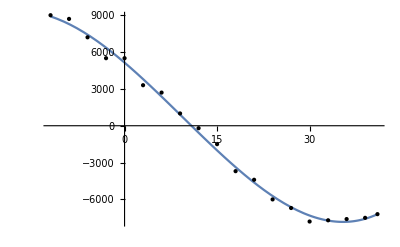

```mathematica
xy={{-12,9000},{-9,8700},{-6,7200},{-3,5500},{0,5500},{3,3300},{6,2700},{9,1000},{12,-200},{15,-1500},{18,-3700},{21,-4400},{24,-6000},{27,-6700},{30,-7800},{33,-7700},{36,-7600},{39,-7500},{41,-7200}};
kploy=Fit[xy,{1,x,x^2,x^3},{x}]
Plot[kploy,{x,-12,41}, Epilog->Point[xy],Axes->{True,True}]
```

```mathematica
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{1,1200,50,1,12000,1}];
Subscript[R, lqr]=DiagonalMatrix[{2,10}];
Subscript[L, 0]=0.20;Subscript[Q, 0]=90;
(*====================系统参数配置====================*)
(*重力加速度*)
g=9.81;
(*连杆长度*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.270;Subscript[L, 3]=0.270;Subscript[L, 4]=0.150;Subscript[L, 5]=0.150;
(*五连杆的质量分布参数*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.135660;Subscript[l, 3]=0.135150;Subscript[l, 4]=0.064820;
Subscript[J, 1]=0.003993;Subscript[J, 2]=0.064379;Subscript[J, 3]=0.060525;Subscript[J, 4]=0.003993;
Subscript[m, 1]=0.211*2;Subscript[m, 2]=0.390*2;Subscript[m, 3]=0.204*2;Subscript[m, 4]=0.211*2;
(*机体的质量分布参数*)
Subscript[L, b]=0.01;(*机体质心相对于关节电机轴平面的高度*)
Subscript[J, b]=0.2997272;(*机体的转动惯量*)
Subscript[m, b]=8.548;(*机体的质量*)
(*驱动轮电机的质量分布参数*)
Subscript[J, wm]=0.000813;
Subscript[m, wm]=0.10*2;(*壳0.1 电机0.38*)
(*驱动轮的质量分布参数*)
Subscript[J, w]=0.004301;(*轮子的转动惯量*)
Subscript[m, w]=0.63*2;(*驱动轮的质量 0.35*)
Subscript[R, w]=0.06;(*轮的半径*)
(*限位*)
upLimit=-23.41;(*上限位*)
downLimit=67.89;(*下限位*)
(*电机半径--画图*)
Subscript[R, jm]=0.045;(*GO8010*)
Subscript[R, wm]=0.0675;(*MF9025*)
Get["VMCsolution.m",Path->NotebookDirectory[]]
SystemCalcu[Q1_,Q2_,Q3_,Q4_,Q5_,Q6_,R1_,R2_]:=(
Module[{},
Subscript[Q, lqr]=DiagonalMatrix[{Q1,Q2,Q3,Q4,Q5,Q6}];
Subscript[R, lqr]=DiagonalMatrix[{R1,R2}];
{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4]}=VMCInverseSolution[Subscript[L, 0],Subscript[Q, 0],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]}][[3]];
(*====================求解等效腿的质量分布====================*)
(*得各质心矢量*)
Subscript[r, 1]={Subscript[l, 1] Cos[Subscript[q, 1]],Subscript[l, 1] Sin[Subscript[q, 1]]};
Subscript[r, 2]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[l, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[l, 2] Sin[Subscript[q, 2]]};
Subscript[r, 3]={Subscript[L, 4] Cos[Subscript[q, 4]]+Subscript[l, 3] Cos[Subscript[q, 3]]+Subscript[L, 5],Subscript[L, 4] Sin[Subscript[q, 4]]+Subscript[l, 3] Sin[Subscript[q, 3]]};
Subscript[r, 4]={Subscript[l, 4] Cos[Subscript[q, 4]]+Subscript[L, 5],Subscript[l, 4] Sin[Subscript[q, 4]]};
Subscript[r, w]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[L, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[L, 2] Sin[Subscript[q, 2]]};
Subscript[m, l]=Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]+Subscript[m, 4]+Subscript[m, wm];
M=Subscript[m, l]+Subscript[m, w]+Subscript[m, b];
Subscript[r, com]=Collect[Expand[Subscript[m, 1] Subscript[r, 1]+Subscript[m, 2] Subscript[r, 2]+Subscript[m, 3] Subscript[r, 3]+Subscript[m, 4] Subscript[r, 4]+Subscript[m, wm] Subscript[r, w]],{Cos[Subscript[q, 1]],Sin[Subscript[q, 1]],Cos[Subscript[q, 2]],Sin[Subscript[q, 2]],Cos[Subscript[q, 3]],Sin[Subscript[q, 3]],Cos[Subscript[q, 4]],Sin[Subscript[q, 4]]}]/Subscript[m, l];
(*求解转动惯量*)
Subscript[d, c1]=Norm[Subscript[r, 1]-Subscript[r, com]];Subscript[J, c1]=Subscript[J, 1]+Subscript[m, 1] Subscript[d, c1]^2;
Subscript[d, c2]=Norm[Subscript[r, 2]-Subscript[r, com]];Subscript[J, c2]=Subscript[J, 2]+Subscript[m, 2] Subscript[d, c2]^2;
Subscript[d, c3]=Norm[Subscript[r, 3]-Subscript[r, com]];Subscript[J, c3]=Subscript[J, 3]+Subscript[m, 3] Subscript[d, c3]^2;
Subscript[d, c4]=Norm[Subscript[r, 4]-Subscript[r, com]];Subscript[J, c4]=Subscript[J, 4]+Subscript[m, 4] Subscript[d, c4]^2;
Subscript[d, cwm]=Norm[Subscript[r, w]-Subscript[r, com]];Subscript[J, cwm]=Subscript[J, wm]+Subscript[m, wm] Subscript[d, cwm]^2;
Subscript[J, com]=Subscript[J, c1]+Subscript[J, c2]+Subscript[J, c3]+Subscript[J, c4]+Subscript[J, cwm];
(*====================腿部模型参数传递====================*)
Subscript[J, l]=Subscript[J, com];
Subscript[L, l]=Subscript[L, 0]-Norm[Subscript[r, com]-{Subscript[L, 5]/2,0}];(*腿的质心的高度*)
(*====================导入模型====================*)
θ=(Subscript[Q, 0]-90)/180*Pi;
Subscript[A, op] = Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op] = Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[C, op] = DiagonalMatrix[{1,1,1,1,1,1}];
Subscript[D, op] = ConstantArray[0,{6,2}];
(*====================LQR控制====================*)
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr];
Return[Subscript[K, lqr]];
];
);
Manipulate[SystemCalcu[Q1,Q2,Q3,Q4,Q5,Q6,R1,R2],{{Q1,1},0,10000},{{Q2,1},0,10000},{{Q3,1},0,1000},{{Q4,1},0,1000},{{Q5,1},0,1000000},{{Q6,1},0,1000},{{R1,1},0,1},{{R2,1},0,1000}](*显示具体数值*)
```

RiccatiSolve::nonnum: RiccatiSolve 接受了一个具有非数值元素的矩阵.